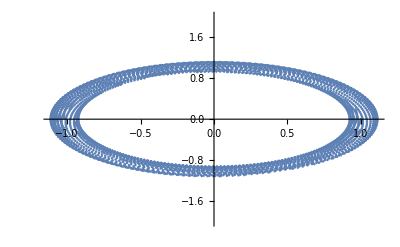

```mathematica
ts=0;tf=100;dt=.03;
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=1;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=2 Pi;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; , {j,2,ll}];
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}],PlotRange->{2,-2}]
```

NOt stable

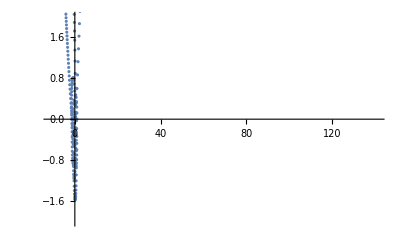
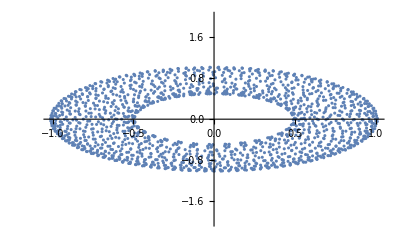
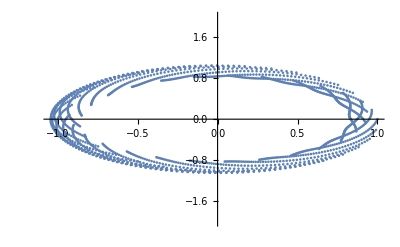
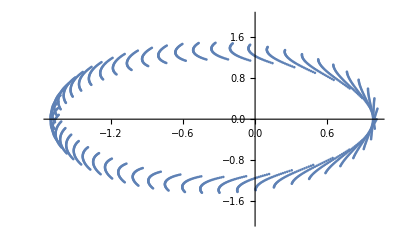
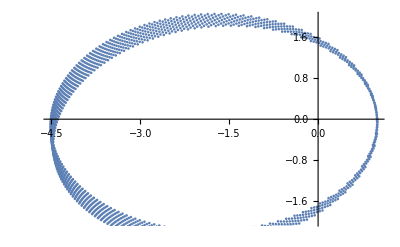

```mathematica
Table[ts=0;tf=50;dt=.03;
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=1;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=v;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; , {j,2,ll}];
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}],PlotRange->{2,-2}],{v,4,8}]
```

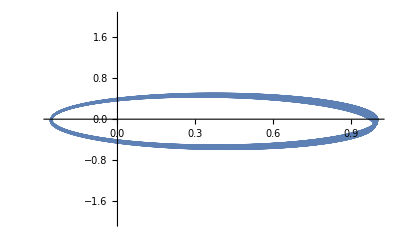
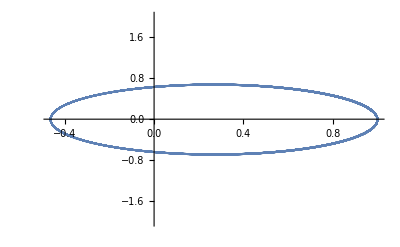
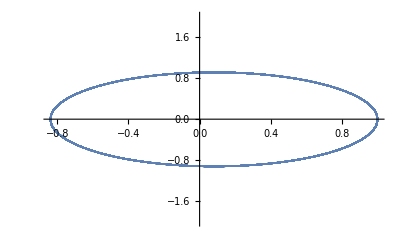
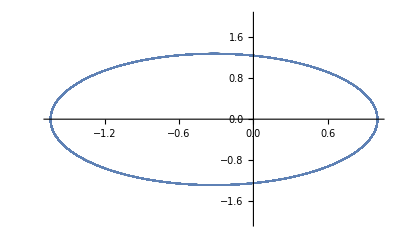
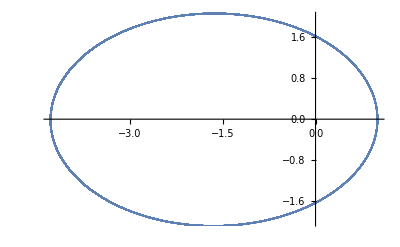

```mathematica
Table[ts=0;tf=100;dt=.001;
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=1;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=v;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; , {j,2,ll}];
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}],PlotRange->{2,-2}],{v,4,8}]
```

```mathematica
(* decrising the time step mak the obbits more stable i,e making the time step .001 instead of 0.03*)
```

```mathematica
Poblem 2
```

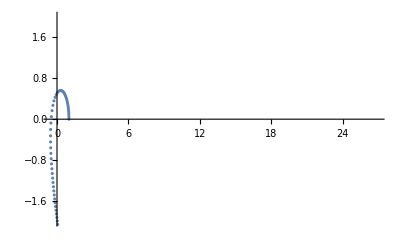
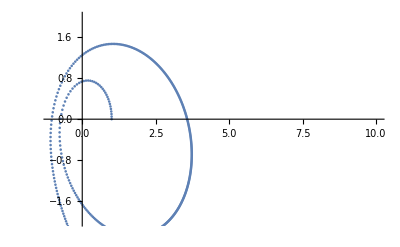
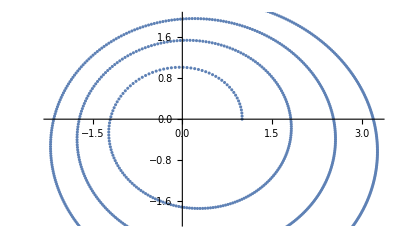
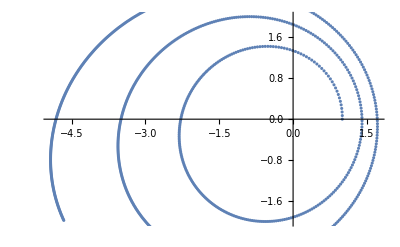
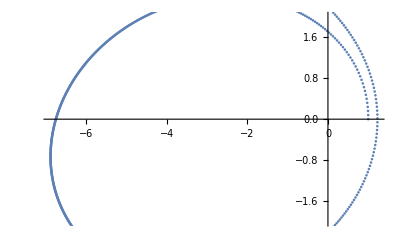

```mathematica
Table[ts=0;tf=10;dt=.01;
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=1;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=v;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j-1]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j-1]] dt; , {j,2,ll}];
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}],PlotRange->{2,-2}],{v,4,8}]
```

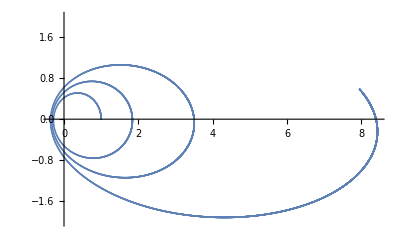
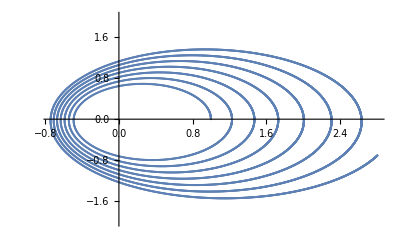
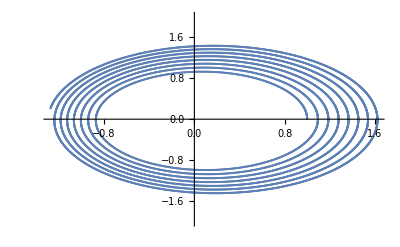
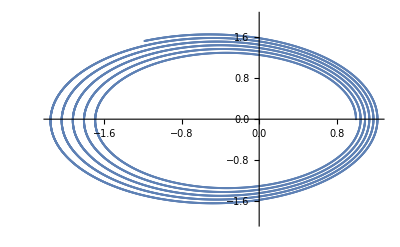
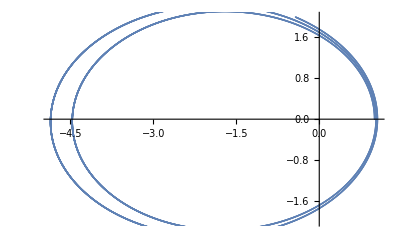

```mathematica
(*comparing this with the previous plots (that used Euler-cromer method) it is clea that Euler method does not work*)
(*for smaller step*)
Table[ts=0;tf=10;dt=.001;
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=1;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=v;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j-1]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j-1]] dt; , {j,2,ll}];
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}],PlotRange->{2,-2}],{v,4,8}]
```

```mathematica
(*time step do not matter*)
```

```mathematica
Problem*3
```

```mathematica
(* kepler law 2 ---- r r dθ/dt= const *)
```

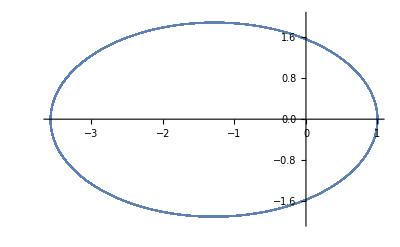

```mathematica
ts=0;tf=10;dt=.001;law={};
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=1;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=2.5Pi;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; 
(*calc the law*)
u2={xl[[j]],yl[[j]]};u1={xl[[j-1]],yl[[j-1]]};
dth=VectorAngle[u1,u2];
law=Append[law,r r dth], {j,2,ll}];
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}],PlotRange->{2,-2}]
```

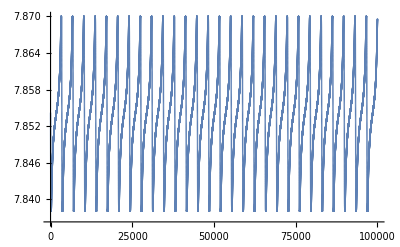

```mathematica
ListPlot[law/dt]
```

```mathematica
(* we can see that within a numerical error of .03 this value is constant and kepler 2 law is satisfied*)
```

```mathematica
(*kepler third law Problem 8*)k3={};
Do[ts=0;tf=6;dt=.001;law={}; rad={};
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=ua;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=2 Pi;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; 


rad=Append[rad,r];
, {j,2,ll}];
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}],PlotRange->{2,-2}]
a=(Min[rad]+Max[rad])/2;
Do[If[rad[[j]]<rad[[j-1]] && rad[[j]]<rad[[j+1]] , t1=j; Break[]],{j,3,Length@rad-2}];
Do[If[rad[[j]]>rad[[j-1]] && rad[[j]]>rad[[j+1]] , t2=j; Break[]],{j,3,Length@rad-2}];
P=Abs[t1-t2] 2  dt;
k3=Append[k3,P^2/a^3];,{ua,.3,1,.2}];k3
```

{0.979379,0.994113,0.994092,0.999718}

```mathematica
(* we notice that this ratio is costant for any a*)
```

0.391349

{0.0077517,0.0380249,0.0432636,0.0510755,0.0635032,0.0840986}

3458

1.00122

```mathematica
(*HAley Comit Problem 4 *)
```

```mathematica
(*
Do[ts=0;tf=42;dt=.001;law={}; rad={};
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=0.59;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=(3.6+0.01 na)* Pi;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; 


rad=Append[rad,r];
, {j,2,ll}];

Do[If[rad[[j]]>rad[[j-1]] && rad[[j]]>rad[[j+1]] , t1=j; Break[]],{j,5,Length@rad-1}];
Do[If[rad[[j]]>rad[[j-1]] && rad[[j]]>rad[[j+1]] , t2=j; Break[]],{j,3,Length@rad-2}];
P=Abs[t1-t2] 2  dt;
If[P>76,Print[(3.68+0.01 na)];Break[]];,{na,1,10}]*)
```

```mathematica
(* with some time of trial and error *)
```

76.706

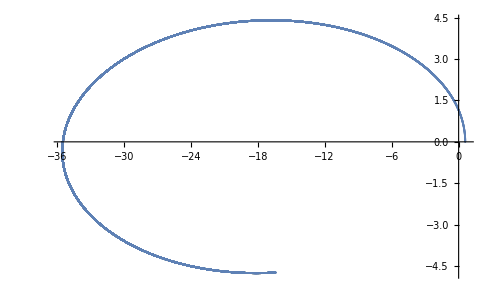

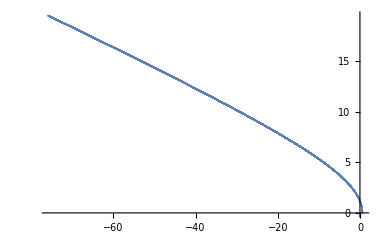

```mathematica
ts=0;tf=70;dt=.001;law={}; rad={};
tl=Range[ts,tf,dt];
ll=Length[tl];
xl=0tl;
xl[[1]]=0.59;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=(3.652)Pi;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ax=-4 Pi^2 xl[[j-1]]/r^3;ay=-4 Pi^2 yl[[j-1]]/r^3;
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; 


rad=Append[rad,r];
, {j,2,ll}];

Do[If[rad[[j]]>rad[[j-1]] && rad[[j]]>rad[[j+1]] , t1=j; Break[]],{j,5,Length@rad-1}];

P=t1 2  dt
ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}]]
```

```mathematica
(*Problem 10*)
```

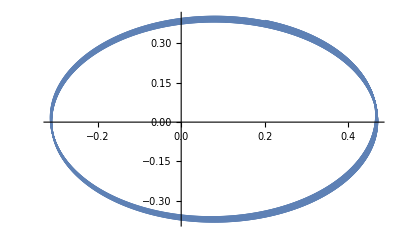

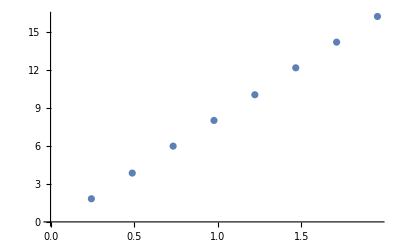

-Graphics-

8.41979

```mathematica
ts=0;tf=2;dt=.0001;b=3;
tl=Range[ts,tf,dt];
ll=Length[tl];
ra=0*tl;
xl=0tl;
xl[[1]]=0.47;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=8.2;α=8*10^-4;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ra[[j-1]]=r;
ax=-4 Pi^2 xl[[j-1]]/r^b(1+α/r^2);ay=-4 Pi^2 yl[[j-1]]/r^b(1+α/r^2);
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; , {j,2,ll}];
ang={1};time={1};Do[ If[ra[[j]]>ra[[j-1]] && ra[[j]]>ra[[j+1]] && ra[[j]]>.39, time=Append[time,dt j];ang=Append[ang,180/Pi VectorAngle[{1,0},{xl[[j]],yl[[j]]}]]];,{j,2,ll}];
data=Table[{time[[j]],ang[[j]]},{j,2,Length[ang]}];
lm=LinearModelFit[data,x,x];
data=Table[{time[[j]],ang[[j]]},{j,2,Length[ang]}];
sl=D[lm[x],x]

ListPlot[Table[{xl[[j]],yl[[j]]},{j,1,ll}]]
ListPlot[Table[{time[[j]],ang[[j]]},{j,2,Length[ang]}]]
```

```mathematica
(*now we reapeat the program for different α *)
```

```mathematica
al={};(*al carry  the value of rate for geven α*)
Do[ts=0;tf=2;dt=.0001;b=3; 
tl=Range[ts,tf,dt];
ll=Length[tl];
ra=0*tl;
xl=0tl;
xl[[1]]=0.47;
yl=0 tl;
yl[[1]]=0;
vx=0 tl;vy=0 tl;
vx[[1]]=0;vy[[1]]=8.2;α=q*10^-4;
Do[r=Norm[{xl[[j-1]],yl[[j-1]]}] ;
ra[[j-1]]=r;
ax=-4 Pi^2 xl[[j-1]]/r^b(1+α/r^2);ay=-4 Pi^2 yl[[j-1]]/r^b(1+α/r^2);
 vx[[j]]=vx[[j-1]]+ax dt;
xl[[j]]=xl[[j-1]]+vx[[j]] dt;
vy[[j]]=vy[[j-1]]+ay dt ;
yl[[j]]=yl[[j-1]] +vy[[j]] dt; , {j,2,ll}];
ang={1};time={1};Do[ If[ra[[j]]>ra[[j-1]] && ra[[j]]>ra[[j+1]] && ra[[j]]>.39, time=Append[time,dt j];ang=Append[ang,180/Pi VectorAngle[{1,0},{xl[[j]],yl[[j]]}]]];,{j,2,ll}];
data=Table[{time[[j]],ang[[j]]},{j,2,Length[ang]}];
lm=LinearModelFit[data,x,x];

sl=D[lm[x],x];al=Append[al,{q*10^-4,sl}],{q,8,14}]
```

```mathematica
al;lm=LinearModelFit[al,x,x];slop=D[lm[x],x];value=slop *1.1* 10^-8
```

0.000120409

```mathematica
ScientificForm[0.0001204087386249217]
```

1.20409×10^-4

```mathematica
(*which is the value we are after*)
```